```mathematica
<<SymbolicComputing`
DateString[]
$Version
$SCVersion
```

Tue 30 May 2023 10:30:11

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

6.0.2 (June 28, 2021)

```mathematica
"11.2.0 for Microsoft Windows (64-bit) (September 11, 2017)"
```

11.2.0 for Microsoft Windows (64-bit) (September 11, 2017)

## Lecture 07 edited by Chi-Ok Hwang, originally made by Dr. 전 경원

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

MathSymbolica Package

Winners of Wolfram Innovator Award 2017

-Graphics-

## Mathematica 프로그래밍 패러다임

-Graphics-

## Symbolic Computing (SC) package

### History

2002. 04: MiscAlgebra Package (MP) Starting to develope
...
2017.      : SC package Commercialization

### Properties

– more than 800 functions
– support for the mathematical writing style
– based on Mathematica
– platform

### Manual

-Graphics-

### Palettes

palette for math input
SCMAF Viewer palette

-Graphics-

Keywords: Notation & Manipulation of Mathematical Expressions

New Notation Using the Traditional Form

• Implemented using the low-level box language
  – MakeBoxes, MakeExpression, ...
  – To be distinguished from the implementation using the Notation Package.

• Delayed on-demand evaluation of the derivatives
  – MPEvaluateD evaluates the derivatives and outputs using the standard notation.
  – MPExpandD expands the derivatives and outputs using the new notation.

• Advantages
  – Improved readability
  – Controlled manipulation of equations involving derivatives
  – Application to mathematical operations like solving differential equations

• Partial derivatives

– Mathematica standard notation

```mathematica
{D[f[x], x], D[f[x, y], x, y], D[f[x, y], x, {y, 2}]}
```

{f'[x],f^(1,1)[x,y],f^(1,2)[x,y]}

– The new notation

```mathematica
{(∂f[x])/(∂x),(∂^2 f[x,y])/(∂x∂y),(∂^3 f[x,y])/(∂x∂y^2)}
SCEvalDeriv[%]
```

{(∂f[x])/(∂x),(∂^2 f[x,y])/(∂x∂y),(∂^3 f[x,y])/(∂x∂y^2)}

{f'[x],f^(1,1)[x,y],f^(1,2)[x,y]}

• Total derivatives

– Mathematica standard notation

```mathematica
Dt[a f[x,t],t]
```

Dt[a,t] f[x,t]+a (f^(0,1)[x,t]+Dt[x,t] f^(1,0)[x,t])

– The new notation

```mathematica
(ⅆ(a f[x,t]))/ⅆt
{SCEvalDeriv[%,Variables->a],SCDerivExpand[%,a]}
```

(ⅆ(a f[x,t]))/ⅆt

{Dt[a,t] f[x,t]+a (f^(0,1)[x,t]+Dt[x,t] f^(1,0)[x,t]),f[x,t] ⅆa/ⅆt+a ((∂f[x,t])/(∂t)+(∂f[x,t])/(∂x) ⅆx/ⅆt)}

### How to Install SymbolicCoputing Package

```mathematica
ToExpression[URLFetch["https://symbcomp.gist.ac.kr/downloads/InstallSymbComp.m"]]
```

```mathematica
Import["https://symbcomp.gist.ac.kr/downloads/InstallSymbComp.m"]
```

```mathematica
Style sheet change
```

In Edit -> Preferences -> Advanced -> Open Option Inspector ->  In Lookup, type “DefaultStyleDefinitions”: Default.nb   -->  SCDefault.nb
or In Format -> Option Inspector ...

```mathematica
How to check your own SC keycode
```

```mathematica
$SCKeycode
```

1cb4061990925f60

## 1 Limits and Continuity

## Lab 0: An Introduction to Mathematica

Wolfram 언어 커널 실행 방법

Solve x^2-3x=-2 for x.

Use factors to solve the equation.

```mathematica
<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]                                (* To use variables with subscripts! *)
Factor[x^2-3x+2]
```

(-2+x) (-1+x)

```mathematica
SCFactor[x^2-3x+2]
```

(-2+x) (-1+x)

Use Solve command.

```mathematica
Solve[x^2-3x==-2,x]
```

{{x→1},{x→2}}

```mathematica
SCSolve[x^2-3x==-2,x]
```

{{x==1},{x==2}}

Solve x^4-3 x^2=4 for real x.

```mathematica
Solve[x^4-3 x^2==4,x]
```

{{x→-2},{x→-ⅈ},{x→ⅈ},{x→2}}

```mathematica
SCSolve[x^4-3 x^2==4,x]
```

{{x==-2},{x==-ⅈ},{x==ⅈ},{x==2}}

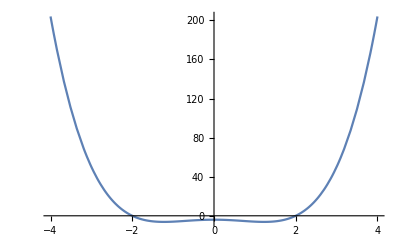

```mathematica
Plot[x^4-3 x^2-4,{x,-4,4}]
```

```mathematica
Solve[x^4-3 x^2==4,x,Reals]
```

{{x→-2},{x→2}}

Find x values of the intersection points of f(x)=14 x^3+2427x-630 and g(x)=781 x^2

```mathematica
Solve[14 x^3+2427x-630==781 x^2,x]
```

{{x→2/7},{x→3},{x→105/2}}

```mathematica
SCSolve[14 x^3+2427x-630==781 x^2,x]
```

{{x==2/7},{x==3},{x==105/2}}

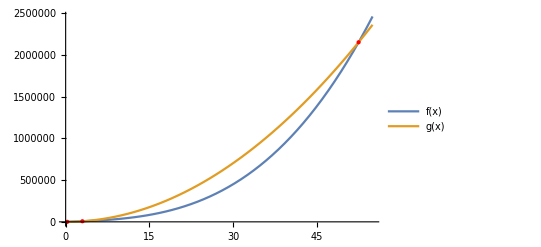

```mathematica
Plot[{14 x^3+2427x-630,781 x^2},{x,0,55},Epilog->{Red,Point[{({x,781 x^2}/.x->2/7),({x,781 x^2}/.x->3),({x,781 x^2}/.x->105/2)}]},PlotLegends->{f[x],g[x]}]
```

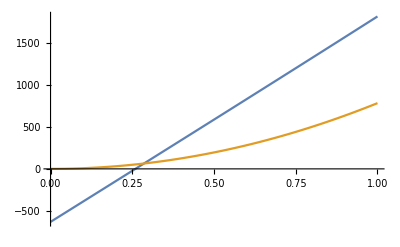
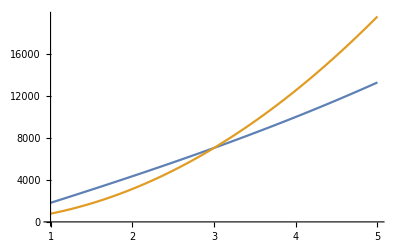
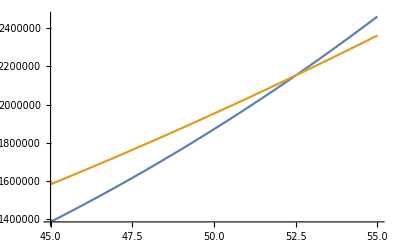

```mathematica
{Plot[#,{x,0,1}],Plot[#,{x,1,5}],Plot[#,{x,45,55}]}&@{14 x^3+2427x-630,781 x^2}
```

Find intersection points of f(x)=sin(x) and g(x)=cos(x) for x between 0 and 2π.

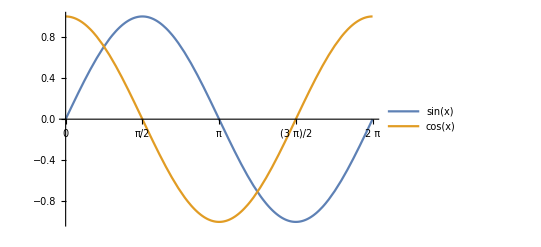

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},Ticks->{{0,π/2,π,3/2 π,2π},Automatic},PlotLegends->"Expressions"]
```

```mathematica
{f[x]==Sin[x],g[x]==Cos[x]}
SCMAF[%,SCEliminate,{All,f[x]==g[x],{f[x],g[x]}},
And,{All,0≤x≤2π},
SCSolve,{All,x},
FullSimplify,{All},Level->{3}]
```

{f[x]==Sin[x],g[x]==Cos[x]}

{{x==-2 ArcTan[1-√2]},{x==2 π-2 ArcTan[1+√2]}}

{{x==π/4},{x==(5 π)/4}}

```mathematica
{f[x]==Sin[x],g[x]==Cos[x]}
SCMAF[%,SCEliminate,{All,f[x]==g[x],{f[x],g[x]}},
And,{All,0≤x≤2π},
SCSolve,{All,x},
FullSimplify,{All},Level->{3}]
```

{f[x]==Sin[x],g[x]==Cos[x]}

{{x==-2 ArcTan[1-√2]},{x==2 π-2 ArcTan[1+√2]}}

{{x==π/4},{x==(5 π)/4}}

Express the above procedure using MathSymbolica package.

```mathematica
<<SymbolicComputing`
```

```mathematica
{f[x]==14 x^3+2427x-630,g[x]==781 x^2}
SCMAF[%,SCEliminate,{All,f[x]==g[x],{f[x],g[x]}},
SCSolve,{All,x}]
```

{f[x]==-630+2427 x+14 x^3,g[x]==781 x^2}

-630+2427 x+14 x^3==781 x^2

{{x==2/7},{x==3},{x==105/2}}

## Practice

```mathematica
(* SCEliminate[eqns, vars]attempts to eliminate variables vars from a set of equations. *)
SCEliminate[{x+y==1,2y==1},y]
```

1/2+x==1

```mathematica
(* SCEliminate[eqns, vars, n]attempts to eliminate variables varsfrom a set of equations using the nth equation. *)   
SCEliminate[{(h c)/λ==(h c)/Subscript[λ, 1]+1/2 m v^2,h/λ==h/Subscript[λ, 1] Cos[θ]+m v Cos[Subscript[θ, e]],h/Subscript[λ, 1] Sin[θ]==m v Sin[Subscript[θ, e]]},v,3]
```

{(c h)/λ==(h^2 Csc[θ_e]^2 Sin[θ]^2)/(2 m λ_1^2)+(c h)/λ_1,h/λ==(h Cos[θ])/λ_1+(h Cot[θ_e] Sin[θ])/λ_1}

```mathematica
(* In the following example,the third equation was used as the argument instead of the index number 3.  *)
SCEliminate[{(h c)/λ==(h c)/Subscript[λ, 1]+1/2 m v^2,h/λ==h/Subscript[λ, 1] Cos[θ]+m v Cos[Subscript[θ, e]],h/Subscript[λ, 1] Sin[θ]==m v Sin[Subscript[θ, e]]},v,h/Subscript[λ, 1] Sin[θ]==m v Sin[Subscript[θ, e]]]
```

{(c h)/λ==(h^2 Csc[θ_e]^2 Sin[θ]^2)/(2 m λ_1^2)+(c h)/λ_1,h/λ==(h Cos[θ])/λ_1+(h Cot[θ_e] Sin[θ])/λ_1}

```mathematica
(*  In the following example,the variable z is eliminated from the equation set by solving the last equation forz.  *)
SCEliminate[{x+y+z==1,x-y==0},y+2z==2,z]
SCEliminate[{x+y+z==1,x-y==0},y+2z==2,z,Solve->{x,y},Keep->True]
```

{x+(2-y)/2+y==1,x-y==0}

{x==0,y==0,y+2 z==2}

```mathematica
(* SCEliminate[expr, eqn, var]attempts to eliminate a variablevarfromexprby using the solution of the equationeqn.  *)
SCEliminate[{f[x]==Sin[x],g[x]==Cos[x]} ,f[x]==g[x],{f[x],g[x]}]
```

Sin[x]==Cos[x]

```mathematica
SCMAF[{f[x]==Sin[x],g[x]==Cos[x]},SCEliminate,{All,f[x]==g[x],{f[x],g[x]}}]
SCSolve[Sin[x]==Cos[x]&& 0≤x≤2π,x] 
% //FullSimplify
```

Sin[x]==Cos[x]

{{x==-2 ArcTan[1-√2]},{x==2 π-2 ArcTan[1+√2]}}

{{4 x==π},{4 x==5 π}}

```mathematica
Solve[Sin[x]==Cos[x] && 0≤x≤2π,x]//FullSimplify
```

{{x→π/4},{x→(5 π)/4}}

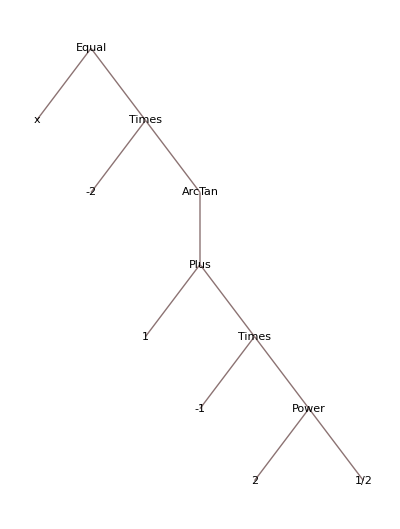

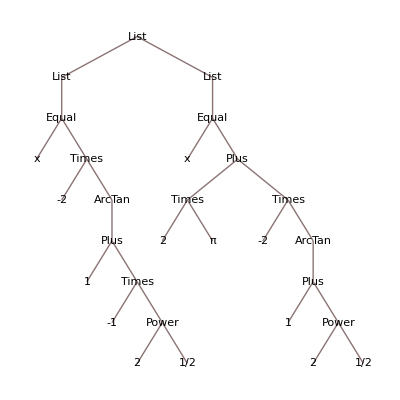

```mathematica
x==-2 ArcTan[1-√2] //TreeForm
{{x==-2 ArcTan[1-√2]},{x==2 π-2 ArcTan[1+√2]}} //TreeForm
```

```mathematica
FullSimplify[x==-2 ArcTan[1-√2] ]
```

4 x==π

```mathematica
Level[x==-2 ArcTan[1-√2],2]
```

{x,-2,ArcTan[1-√2],-2 ArcTan[1-√2]}

```mathematica
{f[x]==Sin[x],g[x]==Cos[x]}
SCMAF[%,SCEliminate,{All,f[x]==g[x],{f[x],g[x]}},
And,{All,0≤x≤2π},
SCSolve,{All,x},
FullSimplify,{All},Level->{3}]
```

{f[x]==Sin[x],g[x]==Cos[x]}

{{x==-2 ArcTan[1-√2]},{x==2 π-2 ArcTan[1+√2]}}

{{x==π/4},{x==(5 π)/4}}

```mathematica
SCEliminate[{f[x]==Sin[x],g[x]==Cos[x]} ,f[x]==g[x],{f[x],g[x]}]
```

Sin[x]==Cos[x]

```mathematica
SCSolve[Sin[x]==Cos[x]&& 0≤x≤2π,x]
```

{{x==-2 ArcTan[1-√2]},{x==2 π-2 ArcTan[1+√2]}}

```mathematica
FullSimplify[%]
```

{{4 x==π},{4 x==5 π}}

```mathematica
Solve[Sin[x]==Cos[x] && 0≤x≤2π,x]
FullSimplify[%]
```

{{x→-2 ArcTan[1-√2]},{x→2 π-2 ArcTan[1+√2]}}

{{x→π/4},{x→(5 π)/4}}

```mathematica
(* Compare Solve with SCSolve *)
```

```mathematica
Solve[{x+y+z==1,x-y==0,y+2z==2},{x,y,z}]
SCSolve[{x+y+z==1,x-y==0,y+2z==2},{x,y,z}]
```

```mathematica
SCEliminate[{x+y+z==1,x-y==0},y+2z==2,z]
SCEliminate[{x+y+z==1,x-y==0,y+2z==2},z]
SCEliminate[{x+y+z==1,x-y==0},y+2z==2,z,Solve->{x,y,z}]
SCEliminate[{x+y+z==1,x-y==0},y+2z==2,z,Solve->{x,y},Keep->True]
```

{{x→0,y→0,z→1}}

{x==0,y==0,z==1}

{x+(2-y)/2+y==1,x-y==0}

{x+(2-y)/2+y==1,x-y==0}

False

{x==0,y==0,y+2 z==2}